{1.,1.,0.6,0.6,0.6,0.36,0.36,0.36,0.216,0.216,0.216,0.1296,0.1296,0.1296,0.07776,0.07776,0.07776,0.046656,0.046656,0.046656,0.0279936,0.0279936,0.0279936,0.0167962,0.0167962,0.0167962,0.0100777,0.0100777,0.0100777,0.00604662}

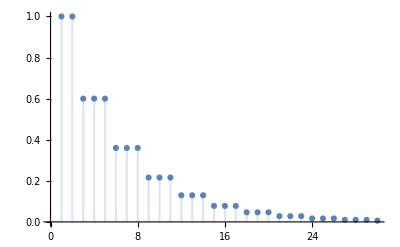

{1.,1.,0.936,0.8976,0.8592,0.8208,0.784858,0.75039,0.717396,0.685878,0.655739,0.626924,0.599376,0.573039,0.547858,0.523784,0.500768,0.478764,0.457726,0.437612,0.418383,0.399998,0.382422,0.365617,0.349552,0.334192,0.319507,0.305467,0.292044,0.279211,0.266942,0.255212,0.243998,0.233276,0.223025,0.213225,0.203856,0.194898,0.186334,0.178146,0.170318,0.162834,0.155679,0.148838,0.142298,0.136045,0.130067,0.124351,0.118887,0.113663}

{FittedModel[ⅇ^(0.0695737-0.0447992 x)],0.999914}

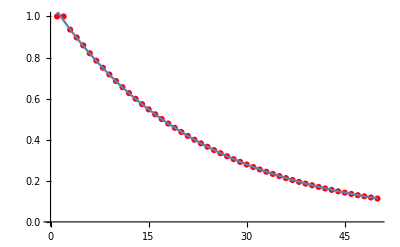

{{3,4},{4,45},{5,126},{6,161},{7,112},{8,45},{9,10},{10,1}}

0.685878

```mathematica
Clear["`*"]
s=3;p=0.6;
(*回合制不刷新*)
SkillTime1[s_,p_,n_]:=p^ Floor[n/s]
Table[SkillTime1[s,p,n],{n,1,30}]
DiscretePlot[SkillTime1[s,p,n],{n,1,30},PlotRange->{0,1}]
(*---------------------------------------------------------------------------*)
(*回合制刷新*)
SkillTime2[s_,p_,n_]:=Block[{M,dis},
M=SparseArray[{Band[{-1,-1}]->1,Band[{2,1}]->1-p},{s+1,s+1}];
M[[1,1;;-2]]=p;
dis=Dot[MatrixPower[M,n],{1}~Join~ConstantArray[0,s]];
1-dis[[-1]]]
ans=Table[SkillTime2[s,p,i],{i,1,50}]
(*FindFit[ans,k/(1+E^(a x +b)),{k,a,b},x]*)
fit=NonlinearModelFit[ans,1/E^(a x +b),{a,b},x];
{fit,fit["RSquared"]}
(*FindFit[ans,E^(a x +b),{a,b},x]*)
Show[ListPlot[ans,PlotStyle->Red],Plot[fit["BestFit"],{x,1,50}]]
(*---------------------------------------------------------------------------*)
(*穷举回合数*)n=10;
(*穷举所有合法组合*)
QST[x_]:=If[Max[Length/@DeleteCases[Split[x,Equal],{1,___}]]≥s,Nothing,x]
(*按触发次数分类*)
QCT[x_]:=Total@Flatten@DeleteCases[Split[x,Equal],{0,___}]
分布=Tally[QCT/@QST/@Tuples[{0,1},n]]
Inner@@Join[{Function[{a,b},b p^a (1-p)^(n-a)]},Transpose@分布,{Plus}]
```

{a[n]==0.6 (8+a[-8+n])+0.4 a[-1+n],a[0]==0.,a[1]==0.6,a[2]==1.44,a[3]==2.376,a[4]==3.3504,a[5]==4.34016,a[6]==5.33606,a[7]==6.33443}

{0.6,1.44,2.376,3.3504,4.34016,5.33606,6.33443,7.33377,8.09351,8.9014,9.78616,10.7247,11.694,12.6792,13.6723,14.6692,15.5238,16.3504,17.2118,18.1196,19.0642,20.0332,21.0167,22.0082,22.9176,23.7772,24.638,25.5269,26.4493,27.3997,28.3699,29.3529,30.2917,31.183,32.056,32.9386,33.845,34.7778,35.733,36.7049,37.657,38.5726,39.4626,40.3482,41.2463,42.1652,43.1059,44.0653,45.0203,45.9517,46.8583,47.7522,48.6487,49.5586,50.487,51.434,52.3858,53.3253,54.2451,55.1494,56.0489,56.9547,57.8741,58.81,59.7555,60.6974,61.626,62.54,63.4454,64.351,65.2648,66.1919,67.1301,68.0705,69.0038,69.9255,70.8374,71.7456,72.6571,73.578,74.5092,75.446,76.3807,77.3076,78.2255,79.1375,80.0493,80.9665,81.8922,82.8244,83.7582,84.6878,85.6104,86.5267,87.4403,88.356,89.2777,90.2057,91.1372,92.0676}

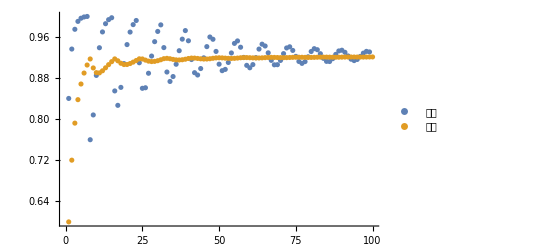

```mathematica
Clear["`*"]
(*Sum[p(1-p)^(k-1)(n-k+1),{k,1,n}]*)
s=8;p=0.6;
st=Inner@@Flatten[{Equal,Transpose@Table[{a[i],i+1-(1-(1-p)^(i+1))/p},{i,0,s-1}],List},1];
eqn={a[n]==p(s+a[n-s])+(1-p) a[n-1]}~Join~st
ans=RecurrenceTable[eqn,a,{n,1,100}]
ListPlot[{Differences[ans],Inner[Divide,ans,Range[1,100],List]},PlotLegends->{"差分","差商"},PlotRange->Full]
```

```mathematica
Clear["`*"]
s=8;p=0.6;
st=Inner[Equal,#[[1]],#[[2]],List]&@Transpose@Table[{a[i],0},{i,0,s-1}];
eqn={a[n]==p(s+a[n-s])+(1-p) a[n-1]}~Join~st;
ans=RSolve[eqn,a[n],n];
Rationalize@Chop@Limit[ans⟦1,1,2⟧/n,n->Infinity]
Rationalize[s p /(p(s-1)+1)]
```

12/13

12/13

```mathematica
Clear["`*"]
s=5;p=0.4;n=20;
M=SparseArray[{Band[{-1,-1}]->1-p,Band[{2,1}]->1-p},{s+1,s+1}];
M[[1,1;;-1]]=p;
dis=NestList[Dot[M,#]&,ConstantArray[0,s]~Join~{1},s];
MatrixForm[aaa=dis~Join~ConstantArray[dis[[-1]],n-s]]
Total[1-aaa[[All,-1]]]
```

(0 | 0 | 0 | 0 | 0 | 1
0.4 | 0. | 0. | 0. | 0. | 0.6
0.4 | 0.24 | 0. | 0. | 0. | 0.36
0.4 | 0.24 | 0.144 | 0. | 0. | 0.216
0.4 | 0.24 | 0.144 | 0.0864 | 0. | 0.1296
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776
0.4 | 0.24 | 0.144 | 0.0864 | 0.05184 | 0.07776)

17.4502

```mathematica
Clear["`*"]
s=5;p=0.4;n=20;
M=SparseArray[{Band[{2,1}]->1},{s+1,s+1}];
M[[1,-2;;-1]]=p;M[[-1,-2;;-1]]=1-p;
M//MatrixForm
dis=NestList[Dot[M,#]&,ConstantArray[0,s]~Join~{1},n];
Total[1-dis[[All,-1]]]
```

(0 | 0 | 0 | 0 | 0.4 | 0.4
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0.6 | 0.6)

15.0213

```mathematica
s=5;p=0.4;n=20;
t=0;
Do[f=RandomChoice[{p,1-p}->{1,0},n+s-1];
Do[If[f[[i]]==1,f[[i+1;;i+s-1]]=0],{i,1,n}];
f=f[[1;;n]];
g=ConstantArray[0,n+s-1];
Do[If[f[[i]]==1,g[[i;;i+s-1]]=1],{i,1,n}];
t+=Total@g[[1;;n]],
{j,1,10000}]
"非覆盖模拟值 = "<>ToString[t/10000.0]
t=0;
Do[g=ConstantArray[0,n+s-1];
f=RandomChoice[{p,1-p}->{1,0},n];
Do[If[f[[i]]==1,g[[i;;i+s-1]]=1],{i,1,n}];
t+=Total@g[[1;;n]],
{j,1,10000}]
"覆盖理论值   = "<>ToString[(-1+p+n p+(1-p)^s (1+p (-1-n+s)))/p]
"覆盖模拟值   = "<>ToString[t/10000.0]
```

非覆盖模拟值 = 15.0509

覆盖理论值   = 17.4502

覆盖模拟值   = 17.4658